```mathematica
DataFileName="/Users/magse/workspace/pcb_layout_demo_eo/BRD1622211227284293.csv";
```

```mathematica
Timing[data=Import[DataFileName];]
```

{13.7099,Null}

```mathematica
PlotSequenceInc[s_,n_]:=Table[Floor[s/n×1/Exp[1]×Exp[x/n]],{x,n}]
```

```mathematica
PlotSequence[s_,n_]:=Join[{1},Accumulate[PlotSequenceInc[s,n]],{s}]
```

```mathematica
LEDColor[r_]:=ColorData["Pastel",r/8.0]
```

```mathematica
PlotFrame[d_]:=Show[Graphics[{LightGreen,Annulus[{0,0},{20,90},{0,π/2}]},Axes->True],Graphics[Table[Partition[{Directive[EdgeForm[Thin],LEDColor[d⟦5+n⟧],Opacity[0.6]],Disk[{d⟦3+n⟧,d⟦4+n⟧},d⟦5+n⟧]},2],{n,1,Length[d]-4,3}],Axes->True],AspectRatio->1,PlotRange->{{0,100},{0,100}},Frame->True,FrameStyle->Directive[GrayLevel[0,0.2],Thickness[Medium],ImageSize->Large]]
```

```mathematica
PlotFrame[data⟦-1⟧]
```

-Graphics-

```mathematica
Do[Block[{frameplot=PlotFrame[data⟦f⟧]},Export[StringReplace[DataFileName,".csv"->"_"<>IntegerString[f,10,8]<>".pdf"],frameplot,"PDF","AllowRasterization"->False]],{f,PlotSequence[Length[data⟦All,1⟧],200]}]
```

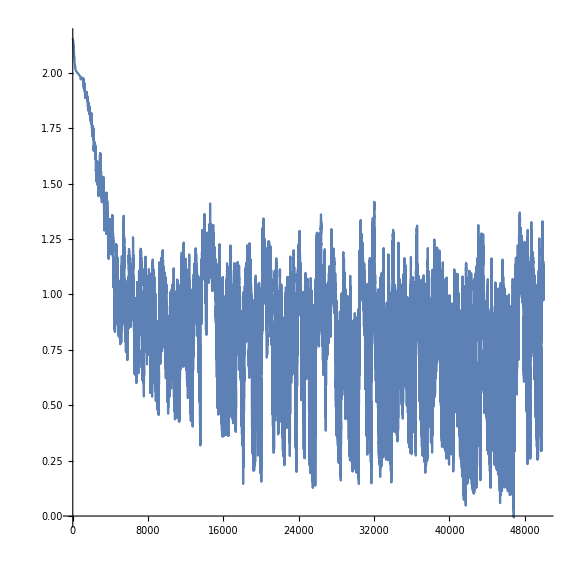

```mathematica
flawplot=ListLinePlot[Log10[data⟦All,2⟧],PlotRange->All,ImageSize->Large,Axes->True,AspectRatio->1,PlotRange->Full]
```

```mathematica
Export[StringReplace[DataFileName,".csv"->"_flaws.pdf"],flawplot,"PDF","AllowRasterization"->False]
```

/Users/magse/workspace/pcb_layout_demo_eo/BRD1622207682575524_flaws.pdf

```mathematica
Timing[Export[StringReplace[DataFileName,".csv"->".mov"],ListAnimate[Table[PlotFrame[data⟦n⟧],{n,1,Length[data⟦All,1⟧],100}],AnimationRate->12,ControlPlacement->Bottom, AppearanceElements->None]]]
```